## Pulsar analysis

```mathematica
Get@"init.m"
""
""
(*These first Four won't work (everywhere?) for some reason, but I can use traditional form anyway. *)
(*Notation[∂f_[x_]/∂x_ ⟸ D[f_,x_]]
Notation[∂^n_ f_[x_]/∂x_^n_ ⟸ D[f_,{x_,n_}]]

Notation[ⅆf_[x_]/ⅆx_ ⟸ Dt[f_][x_]]
Notation[ⅆ^n_ f_[x_]/ⅆ x_^n_ ⟸ Dt[f_][{x_,n_}]]*)

Notation[(∂f_/∂x_)  ⟹ D[f_,x_]]
Notation[(∂^n_ f_/∂x_^n_)  ⟹ D[f_,{x_,n_}]]
Notation[(∂/∂x_)f_  ⟹ D[f_,x_]]
Notation[(∂^n_ /∂x_^n_)f_  ⟹ D[f_,{x_,n_}]]
Notation[∂f_/∂x_  ⟹ D[f_,x_]]
Notation[∂^n_ f_/∂x_^n_  ⟹ D[f_,{x_,n_}]]
Notation[∂/∂x_(f_)  ⟹ D[f_,x_]]
Notation[∂^n_ /∂x_^n_(f_)  ⟹ D[f_,{x_,n_}]]

Notation[(ⅆf_/ⅆx_)  ⟹ Dt[f_,x_]]
Notation[(ⅆ^n_ f_/ⅆ x_^n_)  ⟹ Dt[f_,{x_,n_}]]
Notation[(ⅆ/ⅆx_)f_  ⟹ Dt[f_,x_]]
Notation[(ⅆ^n_/ⅆ x_^n_)f_  ⟹ Dt[f_,{x_,n_}]]


Notation[(∂f_/∂x_)  ⟹ D[f_,x_]]
Notation[(∂^n_ f_/∂x_^n_)  ⟹ D[f_,{x_,n_}]]
Notation[(∂/∂x_)f_  ⟹ D[f_,x_]]
Notation[(∂^n_ /∂x_^n_)f_  ⟹ D[f_,{x_,n_}]]
Notation[∂f_/∂x_  ⟹ D[f_,x_]]
Notation[∂^n_ f_/∂x_^n_  ⟹ D[f_,{x_,n_}]]
Notation[∂/∂x_(f_)  ⟹ D[f_,x_]]
Notation[∂^n_ /∂x_^n_(f_)  ⟹ D[f_,{x_,n_}]]

Notation[(ⅆf_/ⅆx_)  ⟹ Dt[f_,x_]]
Notation[(ⅆ^n_ f_/ⅆ x_^n_)  ⟹ Dt[f_,{x_,n_}]]
Notation[(ⅆ/ⅆx_)f_  ⟹ Dt[f_,x_]]
Notation[(ⅆ^n_/ⅆ x_^n_)f_  ⟹ Dt[f_,{x_,n_}]]
"Notations"
"Notations"
Notation[∂/(∂x_) f_  ⟹ D[f_,x_]]
Notation[(∂f_)/(∂x_)  ⟹ D[f_,x_]]
Notation[(∂^n_ f_)/(∂x_^n_)  ⟹ D[f_,{x_,n_}]]
Notation[∂^n_/(∂x_^n_) f_ ⟹ D[f_,{x_,n_}]]

(* Mixed partials *)
Notation[(∂^2 f_)/(∂x_∂y_) ⟹ D[f_,x_,y_]]

Notation[∂^2/(∂x_∂y_)f_ ⟹ D[f_,x_,y_]]
(* Next two currently don't work *)
(*Notation[(∂^(n_+m_) f_)/(∂x_^n_∂y_^m_) ⟹ D[f_,{x_,n_},{y_,m_}]]
Notation[∂^(n_+m_)/(∂x_^n_∂y_^m_) f_ ⟹ D[f_,{x_,n_},{y_,m_}]]*)
"Fixed notation"
"Fixed notation"
SetOptions[Plot,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,PlotLabels->Automatic];
SetOptions[ListPlot,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,PlotLabels->Automatic];
SetOptions[ContourPlot,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic];
SetOptions[ParametricPlot,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,PlotLabels->Automatic];
SetOptions[ReImPlot,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,PlotLabels->Automatic];
SetOptions[VectorPlot,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic];
SetOptions[DensityPlot,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic];
SetOptions[ComplexPlot,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic];
SetOptions[Plot3D,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,Boxed->False,AxesOrigin->Table[0,3],ViewPoint->{Pi,Pi/2,2},PlotLabels->Automatic,PlotRange->All];
SetOptions[ListPlot3D,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,Boxed->False,AxesOrigin->Table[0,3],ViewPoint->{Pi,Pi/2,2}];
SetOptions[ContourPlot3D,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,Boxed->False,AxesOrigin->Table[0,3],ViewPoint->{Pi,Pi/2,2}];
SetOptions[VectorPlot3D,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,Boxed->False,AxesOrigin->Table[0,3],ViewPoint->{Pi,Pi/2,2}];
SetOptions[SliceVectorPlot3D,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,Boxed->False,AxesOrigin->Table[0,3],ViewPoint->{Pi,Pi/2,2}];
SetOptions[DensityPlot3D,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic Boxed->False,AxesOrigin->Table[0,3],ViewPoint->{Pi,Pi/2,2}];
SetOptions[ComplexPlot3D,AxesStyle->LightGray,TicksStyle->LightGray,AxesLabel->Automatic,Boxed->False,AxesOrigin->Table[0,3],ViewPoint->{Pi,Pi/2,2},PlotRange->All];
"plotting options"
"plotting options"
SetOptions[Manipulate,Paneled->False];
"more options"
"more options"
```

Notations

Notations

Fixed notation

Fixed notation

plotting options

plotting options

more options

more options

### Try to fit in MMA

Get list of x and y values from python

```mathematica
x ={56300.4688155539,56300.45492639893,56300.44103724313,56300.42714808649,56300.413258929024,56300.39936977075,56300.38548061164,56300.37159145176,56300.35770229113,56300.34381312978};
y ={0.0016627957592090326,0.00166282563896264,0.0016628302415629193,0.0016628131097909669,0.0016627781654799023,0.0016627323139534107,0.0016626925155149316,0.0016626750457100386,0.0016626881480292916,0.001662710837899844};
err={2.353097663263867*10^(-9),2.3435228659575588*10^(-9),2.2291472249414805*10^(-9),1.9880488969239098*10^(-9),3.1889485827440945*10^(-9),3.46808484243367*10^(-9),2.1726783415015955*10^(-9),5*10^(-9),2.2821954279209845*10^(-9),3.615634992325844*10^(-9)};

data=Transpose[{x,y}];
```

```mathematica
FindFit[y ,B+A Sin[ω x + ϕ],{B, A, ω, ϕ},x]
```

{B→0.00166275,A→-7.81285×10^-8,ω→0.574299,ϕ→3.12734}

This one comes from python

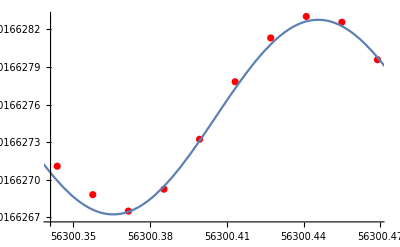

```mathematica
Show[
ListPlot[data,PlotStyle->Red]
,Plot[B+A Sin[ω x + ϕ]/.{B->0.00166275,A ->7.7591 10^-8,ω->2π * 6.25007714, ϕ->-24.3685230},{x,0.32 + 5.63 10^4,0.48 + 5.63 10^4},PlotLabels->None]
]
```

We’ll now attempt to fit better using MMA, and using our found values from python as initial values.

#### No weights

```mathematica
nlm=NonlinearModelFit[data,B+A Sin[ω x + ϕ],{{B,0.00166275},{A,7.7591 10^-8},{ω,2π * 6.25007714},{ϕ,-24.3685230}},x]
```

FittedModel[0.00166275-7.81285×10^-8 Sin[117036.-41.3487 x]]

```mathematica
nlm["BestFit"]
```

0.00166275-7.81285×10^-8 Sin[117036.-41.3487 x]

```mathematica
yWithErr=MapThread[Around,{y,err}];
```

```mathematica
dataWithErr=Transpose[{x,yWithErr}];
```

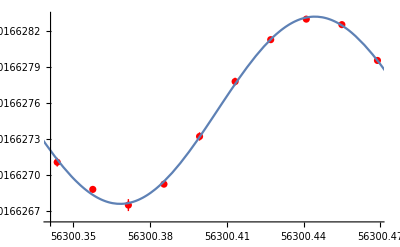

```mathematica
Show[
ListPlot[dataWithErr,PlotStyle->Red]
,Plot[nlm["BestFit"],{x,0.32 + 5.63 10^4,0.48 + 5.63 10^4},PlotLabels->None]
]
```

{5.6886×10^-11,6.36044×10^-10,-1.34404×10^-9,-2.28501×10^-10,2.04978×10^-9,4.53148×10^-10,-2.25744×10^-9,-1.7062×10^-9,4.56825×10^-9,-2.22794×10^-9}

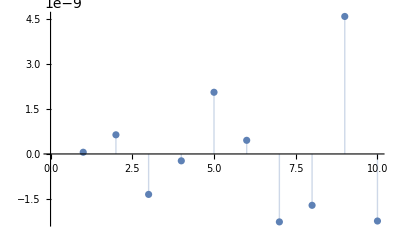

```mathematica
nlm["FitResiduals"]
ListPlot[%,Filling->Axis]
```

```mathematica
nlm["Properties"];
```

```mathematica
Style[nlm["ANOVATable"],Background->White]
```

| DF | SS | MS
Model | 4 | 0.0000276475 | 6.91188×10^-6
Error | 6 | 4.05131×10^-17 | 6.75219×10^-18
Uncorrected Total | 10 | 0.0000276475 | 
Corrected Total | 9 | 3.34502×10^-14 |

```mathematica
Style[nlm["ParameterTable"],Background->White]
```

| Estimate | Standard Error | t-Statistic | P-Value
B | 0.00166275 | 8.29897×10^-10 | 2.00357×10^6 | 1.04347×10^-36
A | 7.81285×10^-8 | 1.1668×10^-9 | 66.9594 | 7.46294×10^-10
ω | 41.3487 | 0.418112 | 98.8939 | 7.20421×10^-11
ϕ | -117036. | 23539.9 | -4.9718 | 0.0025223

#### Using weights err

```mathematica
nlmWeightsErr=NonlinearModelFit[data,B+A Sin[ω x + ϕ],{{B,0.00166275},{A,7.7591 10^-8},{ω,2π * 6.25007714},{ϕ,-24.3685230}},x,Weights->err]
```

FittedModel[0.00166275-7.84907×10^-8 Sin[115563.-41.3226 x]]

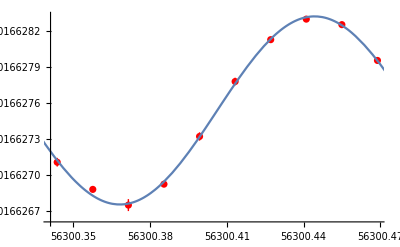

```mathematica
Show[
ListPlot[dataWithErr,PlotStyle->Red]
,Plot[nlmWeightsErr["BestFit"],{x,0.32 + 5.63 10^4,0.48 + 5.63 10^4},PlotLabels->None]
]
```

```mathematica
Style[nlmWeightsErr["ParameterTable"],Background->White]
```

| Estimate | Standard Error | t-Statistic | P-Value
B | 0.00166275 | 8.0565×10^-10 | 2.06387×10^6 | 8.73404×10^-37
A | 7.84907×10^-8 | 1.12952×10^-9 | 69.4906 | 5.97492×10^-10
ω | 41.3226 | 0.399323 | 103.481 | 5.48896×10^-11
ϕ | -115563. | 22482.1 | -5.14023 | 0.00213554

```mathematica
Style[nlmWeightsErr["ParameterConfidenceIntervalTable"],Background->White]
```

| Estimate | Standard Error | Confidence Interval
B | 0.00166275 | 8.0565×10^-10 | {0.00166275,0.00166276}
A | 7.84907×10^-8 | 1.12952×10^-9 | {7.57269×10^-8,8.12545×10^-8}
ω | 41.3226 | 0.399323 | {40.3455,42.2997}
ϕ | -115563. | 22482.1 | {-170575.,-60551.3}

#### Using weights 1 / err

```mathematica
nlmWeightsOneOverErr=NonlinearModelFit[data,B+A Sin[ω x + ϕ],{{B,0.00166275},{A,7.7591 10^-8},{ω,2π * 39/(2π)},{ϕ,1.5}},x,VarianceEstimatorFunction->(1&),Weights->1/err]
```

FittedModel[0.00166275-7.78642×10^-8 Sin[136438.-41.4234 x]]

```mathematica
nlmWeightsOneOverErr["Properties"];
```

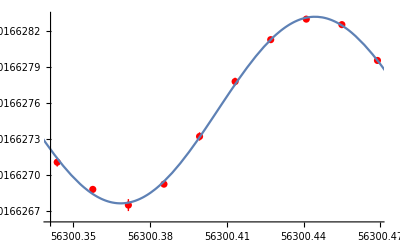

```mathematica
Show[
ListPlot[dataWithErr,PlotStyle->Red]
,Plot[nlmWeightsOneOverErr["BestFit"],{x,0.32 + 5.63 10^4,0.48 + 5.63 10^4},PlotLabels->None]
]
```

```mathematica
Style[nlmWeightsOneOverErr["ParameterTable"],Background->White]
```

| Estimate | Standard Error | t-Statistic | P-Value
B | 0.00166275 | 0.0000165396 | 100.532 | 6.52851×10^-11
A | 7.78642×10^-8 | 0.0000227631 | 0.00342063 | 0.997382
ω | 41.4234 | 8431.25 | 0.00491308 | 0.996239
ϕ | -136438. | 4.74683×10^8 | -0.00028743 | 0.99978

Chi-squared can be obtained from the ANOVA table.

https://mathematica.stackexchange.com/a/240944/73972

Under the Error row, you' ll find

DF : degrees of freedom : 6
SS : Chi^2 : 0.0000452471 ...
MS : Chi^2/dof : 7.54118*10^-6

```mathematica
Style[nlmWeightsOneOverErr["ANOVATable"],Background->White]
```

| DF | SS | MS
Model | 4 | 10451.5 | 2612.87
Error | 6 | 1.52491×10^-8 | 2.54152×10^-9
Uncorrected Total | 10 | 10451.5 | 
Corrected Total | 9 | 0.0000127991 |

```mathematica
χSquared=nlmWeightsOneOverErr["ANOVATableSumsOfSquares"][[2]]
reducedχSquared=nlmWeightsOneOverErr["ANOVATableMeanSquares"][[2]]
```

1.52491×10^-8

2.54152×10^-9

### Repeating the analysis with fit results

```mathematica
nlm["BestFitParameters"]
nlmWeightsErr["BestFitParameters"]
nlmWeightsOneOverErr["BestFitParameters"]
```

{B→0.00166275,A→7.81285×10^-8,ω→41.3487,ϕ→-117036.}

{B→0.00166275,A→7.84907×10^-8,ω→41.3226,ϕ→-115563.}

{B→0.00166275,A→7.78642×10^-8,ω→41.4234,ϕ→-136438.}

```mathematica
δB=nlmWeightsOneOverErr["ParameterErrors"][[1]]LinguisticAssistant
δA=nlmWeightsOneOverErr["ParameterErrors"][[2]]LinguisticAssistant
δω=nlmWeightsOneOverErr["ParameterErrors"][[3]]LinguisticAssistant
δϕ=nlmWeightsOneOverErr["ParameterErrors"][[4]]
```

0.0000165396 s

0.0000227631 s

8431.25 per day

4.74683×10^8

```mathematica
{B,A,ω,ϕ}={B LinguisticAssistant,A LinguisticAssistant,ω LinguisticAssistant,ϕ}/.nlmWeightsOneOverErr["BestFitParameters"]
```

{0.00166275 s,7.78642×10^-8 s,41.4234 per day,-136438.}

```mathematica
B+A Sin[ω t+ϕ];
```

```mathematica
c=LinguisticAssistant;
p=Around[B,δB]+Around[A,δA]
p::usage="This is the period of the sine wave at the highest amplitude";
p0=Around[B,δB]
p0::usage="This is the period at the equilibrium line of the sine wave.";
i(* assumption *)=90°; 
Mp (* assumption *)=LinguisticAssistant ;
```

(0.0016630.000028) s

(0.0016630.000017) s

```mathematica
vs=c(p0/p-1)//UnitConvert[#,"Kilometers"/"Seconds"]&;
v=Abs@vs
```

0.6.10^3 km/s

```mathematica
T=2π/Around[ω,δω] //UnitConvert[#,"Hours"]&
T::usage="The period corresponding to the orbit of the pulsar around the center of mass. It is calculated using the period of the sine wave.";
```

(4.741.) h

```mathematica
ap=(v T)/(2π) (* from v=(2πr)/T *)
ap/LinguisticAssistant
```

0.01.410^7 km

0.38.

```mathematica
Solve[m2^3/(m1+m2)^2==T/(2π G)K1^3,m2]; 
McMin=m2/.First[%/.{m1->Mp,T->T,G->G,K1->Sin[i]v}]
(McMin /LinguisticAssistant )LinguisticAssistant 
McMin/Mp
```

0.02.610^31 kg

(0.13.) M_☉

0.9.

#### Kepler to determine acMin

```mathematica
Solve[T^2/a^3==(4 π^2)/(G(McMin+Mp)),a]//First
a=a/.%/.{G->G,T->T,McMin->McMin,Mp->Mp}//UnitConvert[#,"Kilometers"]&
```

{a→(G^(1/3) T^(2/3) (McMin+Mp)^(1/3))/(2 π)^(2/3)}

0.01.310^8 km

```mathematica
acMin=a-ap//UnitConvert[#,"Kilometers"]&
```

0.01.310^8 km

#### Mass for various inclinations i

```mathematica
ClearAll[i]
```

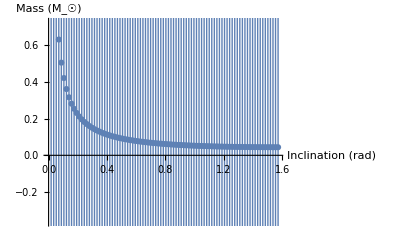

```mathematica
sol=Solve[m2^3/(m1^2(* assuming m1 >> m2 *))Sin[i]^3==T/(2π G)K1^3,m2][[2]];
step=1°;
masses=Table[m2/.sol/.{m1->Mp,T->T,G->G,K1->v},{i,step,90°,step}];
massesMag=QuantityMagnitude[UnitConvert[masses]];
inclinations=Table[i,{i,step,90°,step}];
massData=Transpose[{inclinations,massesMag / LinguisticAssistant}];
ListPlot[massData,AxesLabel->{"Inclination (rad)","Mass (M_☉)"},TicksStyle->Black,Background->White,AxesStyle->Black]
```

Eliminating the assumption that m1 >> m2 gives greater errors for small inclinations.

```mathematica
sol=Solve[m2^3/(m1+m2)^2 Sin[i]^3==T/(2π G)K1^3,m2][[1]];
step=1°;
masses=Table[m2/.sol/.{m1->Mp,T->T,G->G,K1->v},{i,step,90°,step}];
massesMag=QuantityMagnitude[UnitConvert[masses]];
inclinations=Table[i,{i,step,90°,step}];
massData=Transpose[{inclinations,massesMag / LinguisticAssistant}];
ListPlot[massData,AxesLabel->{"Inclination (rad)","Mass (M_☉)"},TicksStyle->Black,Background->White,AxesStyle->Black]
```